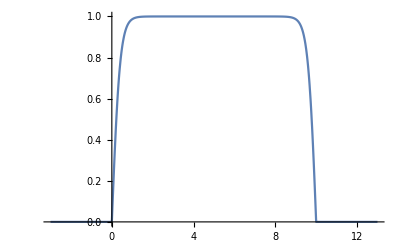

```mathematica
Clear[window]
(*window[t_?NumericQ, τ_, T_] := If[0 < t  < τ, (1 - Cos[π*t/τ])/2, If[(T - τ) < t < T, (1 - Cos[π*(T - t)/τ])/2, 1]]*)
window[t_?NumericQ, τ_, T_] := Piecewise[{{(1 - Cos[π*t/τ])/2, 0 < t < τ}, {(1 - Cos[π*(T - t)/τ])/2, (T - τ) < t < T}, {1, τ ≤ t ≤ T - τ}}, 0]
tanhWindow[t_?NumericQ, τ_, T_] := .5(Tanh[t/(4τ)] - Tanh[(t - T)/(4τ)])
tanhWindow[t_?NumericQ, τ_, T_] := Piecewise[{{(Tanh[t/(4τ)] - Tanh[0/(4τ)] - Tanh[(t - T)/(4τ)] + Tanh[-T/(4τ)]), 0 < t < T}}, 0]
Plot[tanhWindow[t, .1, 10], {t, -3, 13}, PlotRange->All]
```

```mathematica
maxGDUcoefficient[0, .8*.2*1.0056, 200, .0007, 2*10^7, 2*10^7]
```

0.971576

0.971576

```mathematica
NMaximize[{A + B,
-5 < A < 7,
0 < B < 3},
{A, B}]
```

{10.,{A→7.,B→3.}}

```mathematica
Do[(
Tmax = 10^-6;
TimeConstrained[
(
bestT = 0;
bestSoFar = 0;
bestParameters = {};
NMaximize[{
GDUcoefficientAtEnd[ΔEinn, B0inn, Eacinn*Cos[2*π*νE*t]*window[t, 5*10^-9, Tmax] (* + Eacinn2*Cos[2*2*π*νE*t]*), (Eacinn/EoverB)*Cos[2*π*νB*t]*window[t, 5*10^-9, Tmax](* + Bacinn2*Cos[2*2*π*νB*t]*), δinn, δinn(*δEinn, δBinn*)],
-200 ≤ ΔEinn<= 200,
.15 ≤ B0inn <= .2,
-300 ≤ Eacinn <= 300,
(*-50 ≤ Eacinn2 <= 50,*)
(*-.003 ≤ Bacinn <= .003,*)
(*-.0003 ≤ Bacinn2 <= .0003,*)
200000 < EoverB < 300000,
-10*10^7 ≤ δinn <= 10*10^7
(*-10*10^7 ≤ δBinn <= 10*10^7,
-10*10^7 ≤ δEinn <= 10*10^7*)
}
, {ΔEinn, B0inn, Eacinn, (*Eacinn2,*) EoverB, (*Bacinn2,*) δinn },
Method->{"NelderMead", "RandomSeed"->RandomInteger[{0, 10000}]},
MaxIterations->10000
]
),
10000
];
Print["Run " <> ToString[i] <> ": " <> ToString[{bestSoFar, bestParameters, bestT, Tmax}, TraditionalForm]])
,{i, 1000}]
```

Run 1: {0.861631,{-200.,0.154937,-300. cos(3.5689×10^10 t) window(t,1/200000000,1/1000000),-0.00119302 cos(3.54641×10^10 t) window(t,1/200000000,1/1000000),6.76537×10^7,6.76537×10^7},1/1000000,1/1000000}

Run 2: {0.058629,{117.811,0.197225,-288.288 cos(3.5689×10^10 t) window(t,1/200000000,1/1000000),-0.00132476 cos(3.54641×10^10 t) window(t,1/200000000,1/1000000),1.×10^8,1.×10^8},1/1000000,1/1000000}

Run 3: {0.582876,{-69.3245,0.151121,300. cos(2.69814×10^10 t) window(t,1/200000000,1/1000000),0.00117878 cos(2.68035×10^10 t) window(t,1/200000000,1/1000000),8.19868×10^7,8.19868×10^7},1/1000000,1/1000000}

Run 4: {0.00990889,{-123.394,0.187502,220.961 cos(2.5836×10^10 t) window(t,1/200000000,1/1000000),0.000762993 cos(2.56427×10^10 t) window(t,1/200000000,1/1000000),4.07323×10^7,4.07323×10^7},1/1000000,1/1000000}

Run 5: {0.630184,{128.448,0.172166,299.95 cos(3.01314×10^10 t) window(t,1/200000000,1/1000000),0.00132133 cos(2.99517×10^10 t) window(t,1/200000000,1/1000000),3.42888×10^7,3.42888×10^7},1/1000000,1/1000000}

$Aborted

{270.75,0.566727}

6.2×10^-7

{0.0209003,0.515492,0.000753398,0.000643581,0.15478,0.304732,0.00332387,0.000394335}

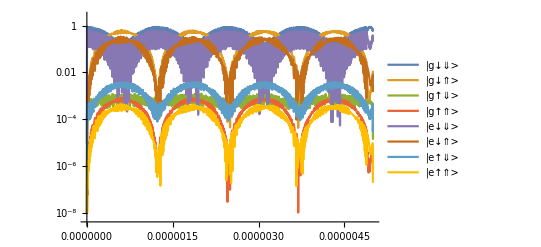

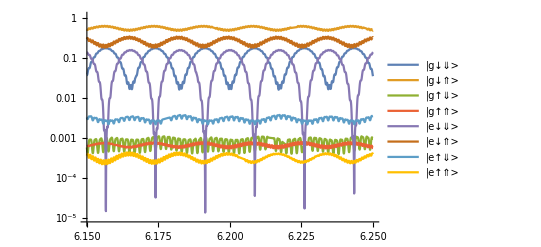

```mathematica
Tmax = 1/200000;

bestSoFar = 0;
maxGDUcoefficient[193.4183611052886,0.1856566598424623,-299.95708738894893 Cos[3.437217116236006*^10 t] window[t,1/200000000,1/200000],-0.0011019959890432411 Cos[3.4165108610083412*^10 t] window[t,1/200000000,1/200000],8.930048574925897*^7,8.930048574925897*^7] // Timing

bestT
state /. {t->bestT}
LogPlot[Evaluate@Table[Max[state[[i]], 10^-8], {i, Length[state]}],{t,0,Tmax}, PlotRange->All, PlotLegends->basisGE]
LogPlot[Evaluate@Table[Max[state[[i]], 10^-8], {i, Length[state]}],{t,bestT - Tmax/1000, bestT + Tmax/1000}, PlotRange->All, PlotLegends->basisGE]
Tmax = 10^-6;
```